-Graphics-

-Graphics-

MaximalBy::dstlms: The requested number of elements 2 is greater than the number of elements 0. Only 0 elements will be returned.

-Graphics-

ImageAssemble::row: Expecting images of the same height in one row.

Show::gcomb: Could not combine the graphics objects in ….

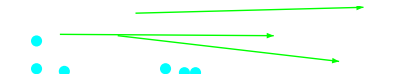
Show[ImageAssemble[{-Graphics-,-Graphics-}],-Graphics-]

```mathematica
(*Notebook to test other built-in functions such as image tracking, edge detection and so on*)

(*Proved to be unsuccessful, objects are not clearly recognised by the routine and takes more time to compute than the previous methods*)img1 = Import["C:\\Users\\Rares\\Desktop\\bubbles\\bubble_sequence\\bubble_sequence_1.jpg"]
img2 = Import["C:\\Users\\Rares\\Desktop\\bubbles\\bubble_sequence\\bubble_sequence_2.jpg"]
e=FindImageShapes[EdgeDetect[img1,10],"Ellipse"];
HighlightImage[img1,Graphics@MaximalBy[e,RegionMeasure,2]]
pts = ImageFeatureTrack[{im1 = img1, im2 = img2}, MaxFeatures -> 20];
Show[ImageAssemble[{im1, im2}], 
 Graphics[{Green, PointSize[.02], 
   MapThread[
    If[#2 === Missing[], {Cyan, Point[#1]}, 
      Arrow[{#1, #2 + {ImageDimensions[im1][[1]], 0}}]] &, pts]}]]
images = {img1, img2};
{w, h} = ImageDimensions[images[[1]]];
res = ImageFeatureTrack[images, 
   Flatten[Table[{x, y}, {x, .5, w - .5, 20}, {y, .5, h - .5, 20}], 
    1]];
```